## Метод скінченних елементів для задачі Пуассона, з умовами Діріхле зліва та Неймана справа ВАРІАНТ № 26 Боровець Роман

-Graphics-

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
f[x_]:=0;
σ[x_]:=0;
μ[x_]:=1;
n= 40;
h = 1.0/n;
g1 = InputFormAssistant;
```

```mathematica
β[x_]:= (-30*(10x-5)) /(1+(10x-5)^2);
```

```mathematica
eqn =- D[μ[x]* D[u[x], x], x] +β[x]* D[u[x], x] + σ[x]* u[x] +NeumannValue[InputFormAssistant, x == 1]  == f[x];
```

```mathematica
"2.      Знайти апроксимацію розв’язку з допомогою вбудованих функцій NDSolve/NDSolveValue"
boundaryConditions = {DirichletCondition[u[x] == 1, x == 0]};
solution = NDSolveValue[{eqn, boundaryConditions}, u, {x, 0, 1}];
```

2.      Знайти апроксимацію розв’язку з допомогою вбудованих функцій NDSolve/NDSolveValue

```mathematica
Plot[solution[x], {x, 0, 1}, PlotRange -> All, AxesLabel -> {"x", "u(x)"}]
```

-Graphics-

```mathematica
improvedFEMImplementation[n_,xvals_, h_]:=Module[{A,l,j,xm, xM},
A=Table[0,{j,0,n},{i,0,n}];
l=Table[0, {j,0,n}];

l[[1]]= 1;(*діріхле*)
A[[1,1]]=1;
A[[1,2]] = 0;   
For[j=1,j <n,j++,
xm = InputFormAssistant;
xM = InputFormAssistant;
A[[j+1,j]]=μ[xm]*(InputFormAssistant)+β[xm]*(InputFormAssistant)+σ[xm]InputFormAssistant;
A[[j+1,j+1]]=μ[xm]InputFormAssistant+β[xm]InputFormAssistant+σ[xm]InputFormAssistant + μ[xM]InputFormAssistant+β[xM]*(InputFormAssistant)+σ[xM]InputFormAssistant ;
A[[j+1,j+2]]=μ[xM]*(InputFormAssistant)+β[xM]InputFormAssistant+σ[xM]InputFormAssistant;
l[[j+1]] = f[xm]InputFormAssistant+f[xM]InputFormAssistant;

];
xm=InputFormAssistant;
l[[n+1]]= f[xm]InputFormAssistant-g1;
A[[n+1, n]]=μ[xm]*(InputFormAssistant)+β[xm]*(InputFormAssistant)+σ[xm]InputFormAssistant;
A[[n+1, n+1]]=μ[xm]*(InputFormAssistant)+β[xm]*(InputFormAssistant)+σ[xm]InputFormAssistant;
Return[{N[A],N[l]}];
];
```

```mathematica
"1.      Знайти апроксимацію розв'язку Методом Скінченних Елементів"
xvals=Table[j/n,{j,0,n}];
{A,l}=improvedFEMImplementation[n,xvals, h ];
uvals=LinearSolve[A,l];
(*A // MatrixForm
l // MatrixForm
Print[uvals];
Print[xvals];*)
ListPlot[Transpose[{xvals,uvals}]]
```

1.      Знайти апроксимацію розв'язку Методом Скінченних Елементів

-Graphics-

```mathematica
Show[Plot[solution[x],{x, 0, 1}],
ListPlot[Transpose[{xvals,uvals}],
PlotStyle->Directive[Orange,PointSize[Large]]]]
```

-Graphics-

```mathematica
sobolevMatrix=1/h{{1,-1},{-1,1}}+h/6{{2,1},{1,2}};
sobolevMatrix // MatrixForm
```

(40.0083 | -39.9958
-39.9958 | 40.0083)

```mathematica
"3.      Обчислити норму Соболєва та Енергетичну норму апроксимацій"
"4.      Вивести графіки апроксимацій та розподілу норм по скінченних елементах"
calcSobolevNorm[α_, n_]:=Table[α[[{j,j+1}]].sobolevMatrix.α[[{j,j+1}]],{j,1,n}];
```

3.      Обчислити норму Соболєва та Енергетичну норму апроксимацій

4.      Вивести графіки апроксимацій та розподілу норм по скінченних елементах

```mathematica
ListPlot[{calcSobolevNorm[uvals,n], calcSobolevNorm[solution[xvals],n]}]
```

-Graphics-

```mathematica
Print["∥u_n∥^2=",Round[Total[calcSobolevNorm[uvals,n]],0.0001]]
Print["∥u∥^2=",Round[Total[calcSobolevNorm[solution[xvals],n]],0.0001]]
```

∥u_n∥^2=5.7559

∥u∥^2=5.4874

```mathematica
energyMatrix[x_]:=Module[{xVal,result},
xVal = N[x + 1/2];
result =  1/h*μ[xVal]{{1,-1},{-1,1}}+InputFormAssistant β[xVal]{{-1,-1},{1,1}}+h/6 σ[xVal]{{2,1},{1,2}};

 Return[result];
];
```

```mathematica
calcEnergyNorm[α_,n_]:=Table[α[[{j,j+1}]].energyMatrix[α[[j]]].α[[{j,j+1}]],{j,1,n}];
ListPlot[{calcEnergyNorm[uvals,n], calcEnergyNorm[solution[xvals],n]}]
```

-Graphics-

```mathematica
Print[Total[calcEnergyNorm[uvals,n]]]
Print[Total[calcEnergyNorm[solution[xvals],n ]]]
```

0.0901407

-0.0152474

```mathematica
"5.      Виконати описані вище кроки для різної кількості скінченних елементів

6.      Починаючи з n=4 та збільшуючи кількість скінченних елементів вдвічі на кожній ітерації знайти таке N при якому різниця по модулю норми Соболєва між двома ітераціями менша ніж 10-3.

7.      Вивести табличку, де кожен рядок відповідає певній ітерації, яка містить наступні значення: кіль-сть скінченних елементів, значення Енергетичної норми та норми Соболєва.

8.      Вивести графік значень норм (Соболєва та Енергетичної) для усіх ітерацій "
```

5.      Виконати описані вище кроки для різної кількості скінченних елементів

6.      Починаючи з n=4 та збільшуючи кількість скінченних елементів вдвічі на кожній ітерації знайти таке N при якому різниця по модулю норми Соболєва між двома ітераціями менша ніж 10-3.

7.      Вивести табличку, де кожен рядок відповідає певній ітерації, яка містить наступні значення: кіль-сть скінченних елементів, значення Енергетичної норми та норми Соболєва.

8.      Вивести графік значень норм (Соболєва та Енергетичної) для усіх ітерацій

Iteration 0: N =4, Energy Norm =0.06862, Sobolev Norm =0.16585

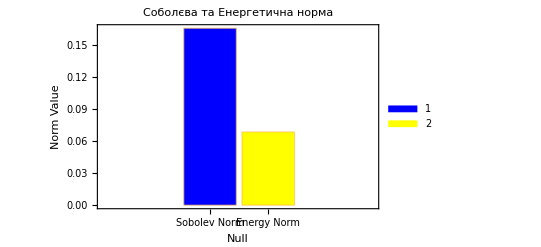

Iteration 1: N =8, Energy Norm =45.7648, Sobolev Norm =48.9877

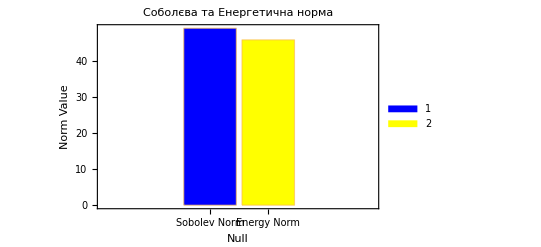

Iteration 2: N =16, Energy Norm =0.48394, Sobolev Norm =0.80914

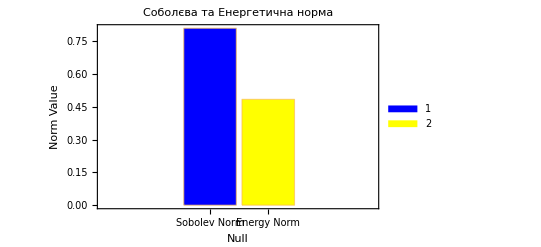

Iteration 3: N =32, Energy Norm =0.03028, Sobolev Norm =0.19522

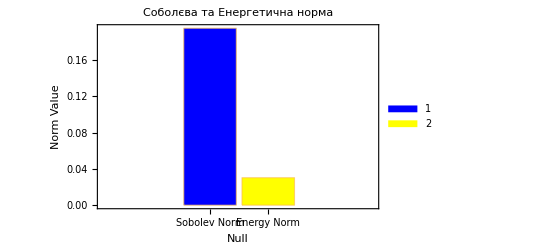

Iteration 4: N =64, Energy Norm =-0.01738, Sobolev Norm =0.09217

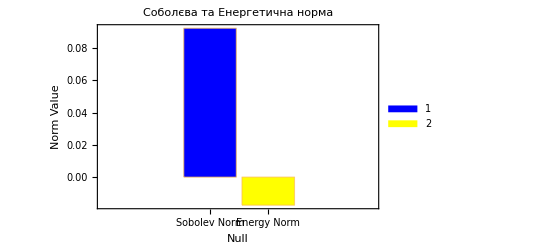

Iteration 5: N =128, Energy Norm =-0.01606, Sobolev Norm =0.06863

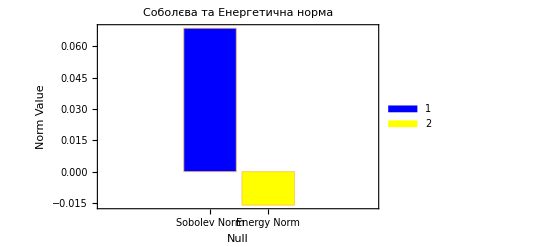

Iteration 6: N =256, Energy Norm =-0.00984, Sobolev Norm =0.06287

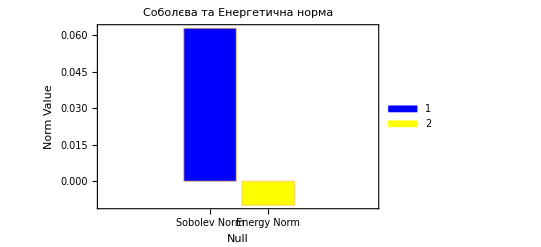

Iteration 7: N =512, Energy Norm =-0.00538, Sobolev Norm =0.06144

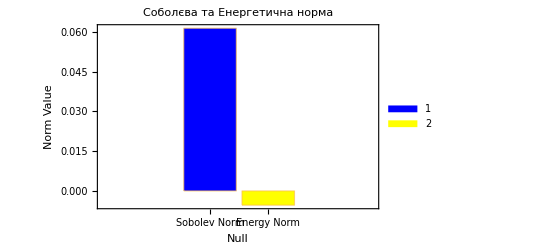

Iteration 8: N =1024, Energy Norm =-0.0028, Sobolev Norm =0.06108

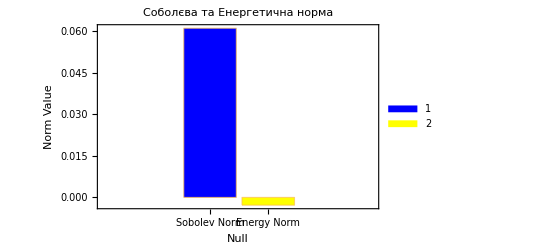

```mathematica
nincrement=4;
prevSobolevNorm=0;
sobolevNorm=0;
prevEnergyNorm = 0;
energyNorm = 0;
iteration=0;
table = {};
sobolevNormsList={};
energyNormsList={};
While [True,
xvalsi=Table[InputFormAssistant,{j,0,nincrement}];
{A,l}=improvedFEMImplementation[nincrement,xvalsi,1/nincrement ];
uvalsi=LinearSolve[A,l];
sobolevNorm=calcSobolevNorm[uvalsi,nincrement];
energyNorm=calcEnergyNorm[uvalsi,nincrement];
sobolevNormT=Round[Total[sobolevNorm]/nincrement,0.00001];
energyNormT=Round[Total[energyNorm]/nincrement,0.00001];
Print["Iteration ",Length[table],": N =",nincrement,", Energy Norm =",energyNormT,", Sobolev Norm =",sobolevNormT];
aproximationN =ListPlot[Transpose[{xvalsi,uvalsi}],PlotLabel->"Апроксимація для певного n"];
normsToElement =ListPlot[{sobolevNorm, energyNorm},PlotLabel->"Розподілу норм по скінченних елементах",Frame -> True,
    FrameLabel -> {, "Norm Value"},
    PlotLegends -> {"Sobolev Norm", "Energy Norm"}];
Print[BarChart[Transpose[{sobolevNormT,energyNormT}],ChartLabels->{"Sobolev Norm","Energy Norm"},PlotLabel->"Соболєва та Енергетична норма",ChartLegends->{"Sobolev Norm","Energy Norm"},Frame->True,FrameLabel->{,"Norm Value"},ChartStyle -> {Blue,Yellow}]];
AppendTo[table,{nincrement,sobolevNormT,energyNormT,aproximationN, normsToElement}];
AppendTo[sobolevNormsList,sobolevNormT];
AppendTo[energyNormsList,energyNormT];
If[Abs[sobolevNormT-prevSobolevNorm]<10^-3,Break[]];
prevSobolevNorm=sobolevNormT;
prevEnergyNorm = energyNormT;
nincrement*=2;
];
```

Через те що є обмеження на пам'ять я не зміг запхати графік в таблицю тому вивів в прінт(можливо це лише в вебі)

```mathematica
TableForm[table,TableHeadings->{None,{"Number of Elements (N)","Energy Norm","Sobolev Norm","AproximationToN","NormsToElement","Norms"}}]
```

Number of Elements (N) | Energy Norm | Sobolev Norm | AproximationToN | NormsToElement
4 | 0.16585 | 0.06862 | -Graphics- | -Graphics-
8 | 48.9877 | 45.7648 | -Graphics- | -Graphics-
16 | 0.80914 | 0.48394 | -Graphics- | -Graphics-
32 | 0.19522 | 0.03028 | -Graphics- | -Graphics-
64 | 0.09217 | -0.01738 | -Graphics- | -Graphics-
128 | 0.06863 | -0.01606 | -Graphics- | -Graphics-
256 | 0.06287 | -0.00984 | -Graphics- | -Graphics-
512 | 0.06144 | -0.00538 | -Graphics- | -Graphics-
1024 | 0.06108 | -0.0028 | -Graphics- | -Graphics-

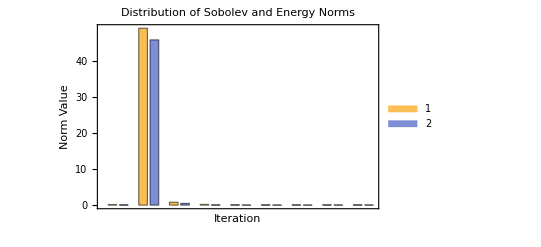

```mathematica
BarChart[Transpose[{sobolevNormsList,energyNormsList}],ChartLabels->{"Sobolev Norm","Energy Norm"},PlotLabel->"Distribution of Sobolev and Energy Norms",ChartLegends->{"Sobolev Norm","Energy Norm"},Frame->True,FrameLabel->{"Iteration","Norm Value"}]
```